G:\LAT\sd_metropolis\data\pcm_wc_mspace\scalars_d2_t54_s108_l3.0120.dat

681 data points, normalization factor is 9638.18

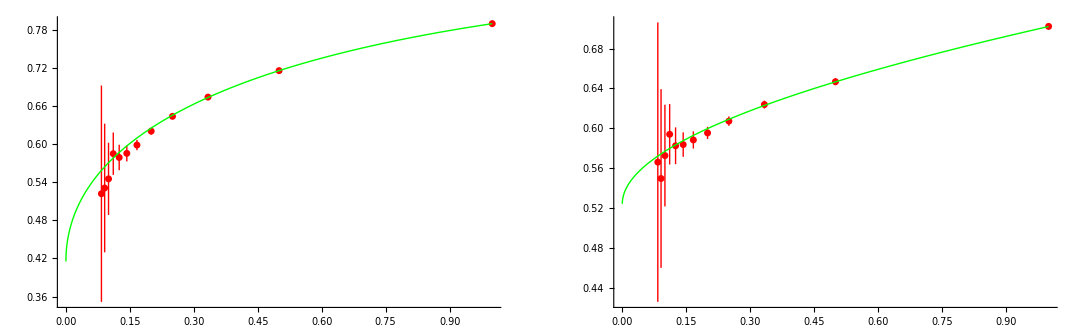

Mean link is 0.524059 +/- 0.017104

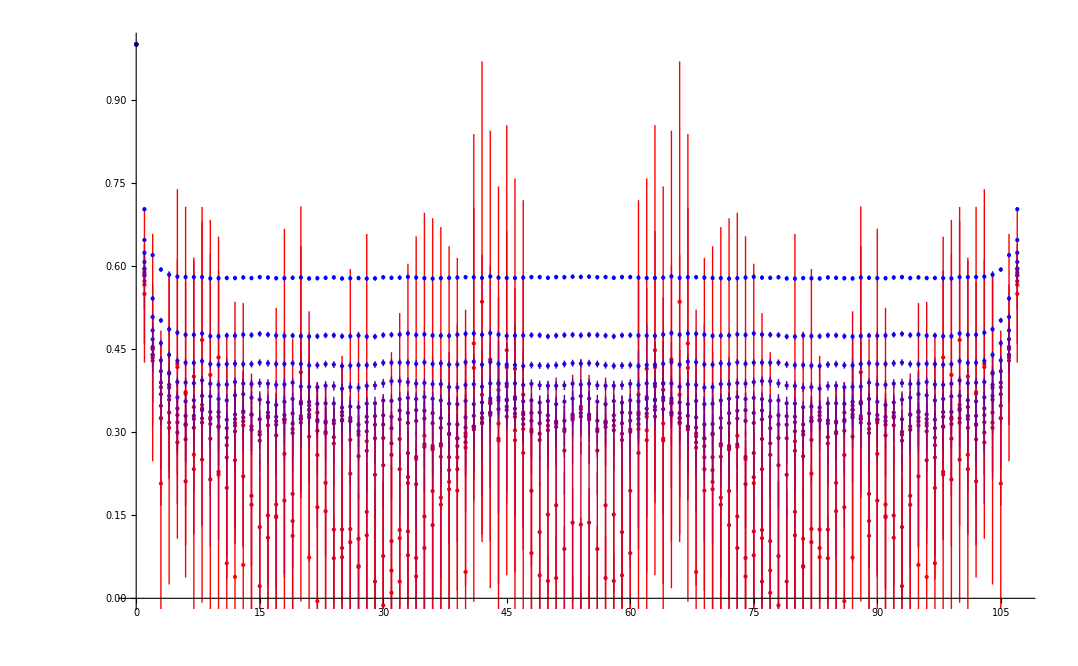

```mathematica
(* Unifying all the scripts *)
Get["G:\\LAT\\sd_metropolis\\convergence_analysis.m"];
Get["G:\\LAT\\sd_metropolis\\apps\\pcm_wc_mspace\\pcm_wc_mspace_tuning.m"];
(* Simulation parameters *)
λ=3.0120; LT=54; LS=108; mmax=11;
Suffix="d2_t"<>ToString[LT]<>"_s"<>ToString[LS]<>"_l"<>fsndig[λ,4];
ScalarFileName="G:\\LAT\\sd_metropolis\\data\\pcm_wc_mspace\\scalars_"<>Suffix<>".dat";
Print[ScalarFileName];
(* Importing the scalar data, obtaining the mean values and the correlation matrices *)
ScalarData=Import[ScalarFileName,"Table"];
np=Quotient[Length[ScalarData],mmax+1];
{GxMean,GxCorrelationMatrix}=XYCorrelatedDataStatistics[ScalarData,2,(mmax+1)];
{LinkMean,LinkCorrelationMatrix}=XYCorrelatedDataStatistics[ScalarData,4,(mmax+1)];
(* Now calculating the normalization factor basing on the first nontrivial order for Gx *) (* TODO: implement also leading order for the link and NL0 for link and Gx - to control the goodness *)
Gx0=GxOrder0[LT,LS,λ];
NFactor=(Gx0-1)/GxMean[[1]];
Print[np," data points, normalization factor is ",NFactor];
(* Rescale all the data properly *)
{GxMean,LinkMean}=1+NFactor {GxMean,LinkMean};
{GxCorrelationMatrix,LinkCorrelationMatrix}*=NFactor^2;
(* Fitting and extrapolating *)
xs=Table[1/(m+1),{m,0,mmax}];
Clear[x];
FitFuncs={1,√x,x};
{GxExtrapolation,GxExtrapolationCovariance}=FitCorrelatedData[xs,GxMean,GxCorrelationMatrix,FitFuncs,x];
{LinkExtrapolation,LinkExtrapolationCovariance}=FitCorrelatedData[xs,LinkMean,LinkCorrelationMatrix,FitFuncs,x];
(* Plots for the scalar data *)
GrGxData=PlotWithErrors[xs,GxMean,Sqrt[Diagonal[GxCorrelationMatrix]],PlotRange->{{0.0,All},{0.0,All}},PlotStyle->{Red,PointSize[0.01]}];
GrLinkData=PlotWithErrors[xs,LinkMean,Sqrt[Diagonal[LinkCorrelationMatrix]],PlotRange->{{0.0,All},{0.0,All}},PlotStyle->{Red,PointSize[0.01]}];
Clear[x];
GrGxExtrapolation=Plot[Sum[GxExtrapolation[[i]]FitFuncs[[i]],{i,1,Length[FitFuncs]}],{x,0,1},PlotRange->All,PlotStyle->{Green}];
GrLinkExtrapolation=Plot[Sum[LinkExtrapolation[[i]]FitFuncs[[i]],{i,1,Length[FitFuncs]}],{x,0,1},PlotRange->All,PlotStyle->{Green}];
GraphicsGrid[{{Show[GrGxData,GrGxExtrapolation,ImageSize->500],Show[GrLinkData,GrLinkExtrapolation,ImageSize->500]}}]
Print["Mean link is ",LinkExtrapolation[[1]]," +/- ",√LinkExtrapolationCovariance[[1,1]] ];
(* Importing the correlators *)
xs=Table[x,{x,0,LS-1}];
GrS={};
For[m=0,m≤mmax,m++,
r=m/mmax;
GxyDataFile="G:\\LAT\\sd_metropolis\\data\\pcm_wc_mspace\\Gxy_"<>Suffix<>"_o"<>ToString[m]<>".dat";
(*Print[GxyDataFile];*)
GxyData=Import[GxyDataFile,"Real32"];
GxyData=Partition[GxyData,LS];
np1=Length[GxyData];
If[np1≠np,Print[Style["The number of data points in the correlator do not match the number of data points in scalars ",FontColor->Red],np1," ",np];];
{aGxy,dGxy}=1/np1 Sum[
cGxy=Re[Fourier[GxyData[[ip]],FourierParameters->{1,1}]];
{cGxy,cGxy^2}
,{ip,1,Length[GxyData]}];
dGxy=√((dGxy-aGxy^2)/(np1-1));
aGxy=1 + NFactor aGxy;
dGxy = NFactor dGxy;
AppendTo[GrS,PlotWithErrors[xs,aGxy,dGxy,PlotStyle->{RGBColor[r,0,1-r]},PlotRange->{0.0,1.0}]];
];
Show[Reverse[GrS]]
```